# Kb-sample dwell-fatigue evaluation code

## Data import

## Clarify file content

```mathematica
DwellData=ImportString[StringReplace[Import[NotebookDirectory[]<>"RawData.csv","Text"],
{","->".",";"->","}]];(*Depending on what your file looks like you might want need to use StringReplace*)
TableForm[%[[2;;5]],TableHeadings->{None,%[[1]]}]
```

## Calibration curve data

```mathematica
b=5.992; (*Calibration curve data*)
d=5.904; (*Calibration curve data*)
(*PDpre=0.307; (*the last PD of pre-crack measurement [v]*)*)
```

## Functions

```mathematica
AveragePotential[PotentialMax_,PotentialMin_]:=(PotentialMax+PotentialMin)/2;
PotentialDropOverCrack[averagePotential_,potentialDropStartValue_]:=averagePotential-potentialDropStartValue;
CrackArea[potentialDropOverCrack_,b_,d_]:=b*potentialDropOverCrack+d*potentialDropOverCrack^2; (* Add reference if possible *)
TotalCrackArea[crackArea_,an_,cn_]:=crackArea+π/2*an*cn; (* Crack area + notch area *)
CrackLength[totalCrackArea_]:=√((2*totalCrackArea)/π);
```

## Constants

```mathematica
ConstantsFilePath=NotebookDirectory[]<>"Constants.xls";
```

```mathematica
T=Import[ConstantsFilePath][[1,4,2]](*Specimen thickness [mm]*)
```

```mathematica
W=Import[ConstantsFilePath][[1,5,2]] (*Specimen width [mm]*)
```

```mathematica
an=Import[ConstantsFilePath][[1,42,2]](*Notch dimension*)
```

```mathematica
cn=Import[ConstantsFilePath][[1,43,2]] (*Notch dimension*)
```

```mathematica
PD0pre=Import[ConstantsFilePath][[1,12,1]]  (*the average of PDs of pre-crack measurement [V]*)
```

## Calculations

```mathematica
DwellDataBlock10=Select[DwellData,#[[5]]==10&];(*Read in the the values you need i.e., start value an so forth*)
{#[[4]]-%[[1,4]],AveragePotential[#[[9]],#[[9]]]}&/@%[[;;;;10]];
{#[[1]],PotentialDropOverCrack[#[[2]],PD0pre]}&/@%;
{#[[1]],CrackArea[#[[2]],b,d]}&/@%;
{#[[1]],TotalCrackArea[#[[2]],an,cn]}&/@%;
{#[[1]],CrackLength[#[[2]]]}&/@%;
cycleVsCrack=%;
ListPlot[cycleVsCrack,PlotLabel->Style["Dwell, Temp °C, Dwell-time, MPa", FontSize->12],PlotLegends->{"Dwell, Temp °C, Dwell-time, MPa"},
PlotRange->Full,
AxesLabel->{"Cycle (N)" ,"Crack length a (mm)"}]
```

```mathematica
ListPlot[cycleVsCrack[[1;;500;;10]],(*check data*)PlotLabel->Style["Dwell, Temp °C, Dwell-time, MPa", FontSize->12],PlotLegends->{"Dwell, Temp °C, Dwell-time, MPa"},AxesLabel->{"Cycle (N)" ,"Crack length a (mm)"}]
```

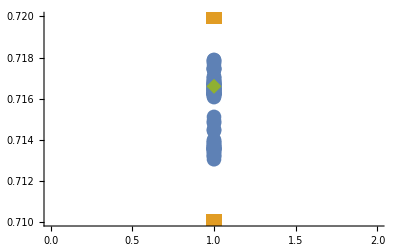

```mathematica
roundedCycleVsCrack={#[[1]],Round[#[[2]],0.01]}&/@cycleVsCrack; (*rounding data*)
roundedMeanCyclePerCrackLength ={#[[1,1]],Mean[#[[;;,2]]]}&/@Gather[roundedCycleVsCrack[[;;;;1]],#1[[1]]==#2[[1]]&];
ListPlot[{Select[cycleVsCrack,#[[1]]==1&],
Select[roundedCycleVsCrack,#[[1]]==1&],Select[roundedMeanCyclePerCrackLength,#[[1]]==1&]}, 
PlotRange->Full,
PlotMarkers->{Automatic,15}]
```

```mathematica
MeanForceMax=Mean[DwellDataBlock10[[2;;,8]]]*1000;
MeanForceMin=Mean[DwellDataBlock10[[2;;,9]]]*1000;
dS=(MeanForceMax-MeanForceMin)/(T*W)*1000000; 
dSMax=MeanForceMax/(T*W)*1000000;
```

```mathematica
M[a_]:=1.04+0.202*(a/T)^2-0.106*(a/T)^4;
DeltaK[a_]:=dS*√(π*a/1000)*M[a]/1.57/1000000;
```

## This is the interesting part

```mathematica
crackLengthPerCycleInterpolationSimple=LinearModelFit[{#[[1]],#[[2]]}&/@roundedMeanCyclePerCrackLength[[;;;;1]],{1,x,x^2,x^3,x^4,x^5},x]
Show[{
ListPlot[roundedMeanCyclePerCrackLength[[;;;;30]],AxesLabel->{"Cycle (N)", "a"},PlotMarkers->{Automatic,10}],
Plot[crackLengthPerCycleInterpolationSimple[x],{x,0,3000},PlotStyle->Red] (*Fits a curve to your data*)
}]
```

```mathematica
NadadN=Table[{x,crackLengthPerCycleInterpolationSimple[x],crackLengthPerCycleInterpolationSimple'[x]},{x,0,3000,30}];
```

```mathematica
ListLogLogPlot[{DeltaK[#[[2]]],#[[3]]}&/@NadadN,PlotMarkers->{Automatic,10},AxesLabel->{"ΔK","da/dN"}]
Export[NotebookDirectory[]<>"DwellDaDnDeltaK.pdf",%]
Export[NotebookDirectory[]<>"DwellDaDnDeltaK.xlsx",{DeltaK[#[[2]]],#[[3]]}&/@NadadN]
```

```mathematica
crackLengthPerTimeInterpolationSimple=LinearModelFit[{#[[1]]*2162,#[[2]]}&/@roundedMeanCyclePerCrackLength[[;;;;1]],{1,x,x^2,x^3,x^4,x^5},x]
Plot[crackLengthPerTimeInterpolationSimple[x],{x,0,3000*2162}]
```

```mathematica
tadadN=Table[{x,crackLengthPerTimeInterpolationSimple[x],crackLengthPerTimeInterpolationSimple'[x]},{x,0,3000*2162,30*2162}];
```

```mathematica
ListLogLogPlot[{DeltaK[#[[2]]],#[[3]]}&/@tadadN,PlotMarkers->{Automatic,10},AxesLabel->{"ΔK","da/dt"}]
Export[NotebookDirectory[]<>"DwellDaDtKmax.pdf",%]
Export[NotebookDirectory[]<>"DwellDaDtKmax.xlsx",{DeltaK[#[[2]]],#[[3]]}&/@tadadN]
```